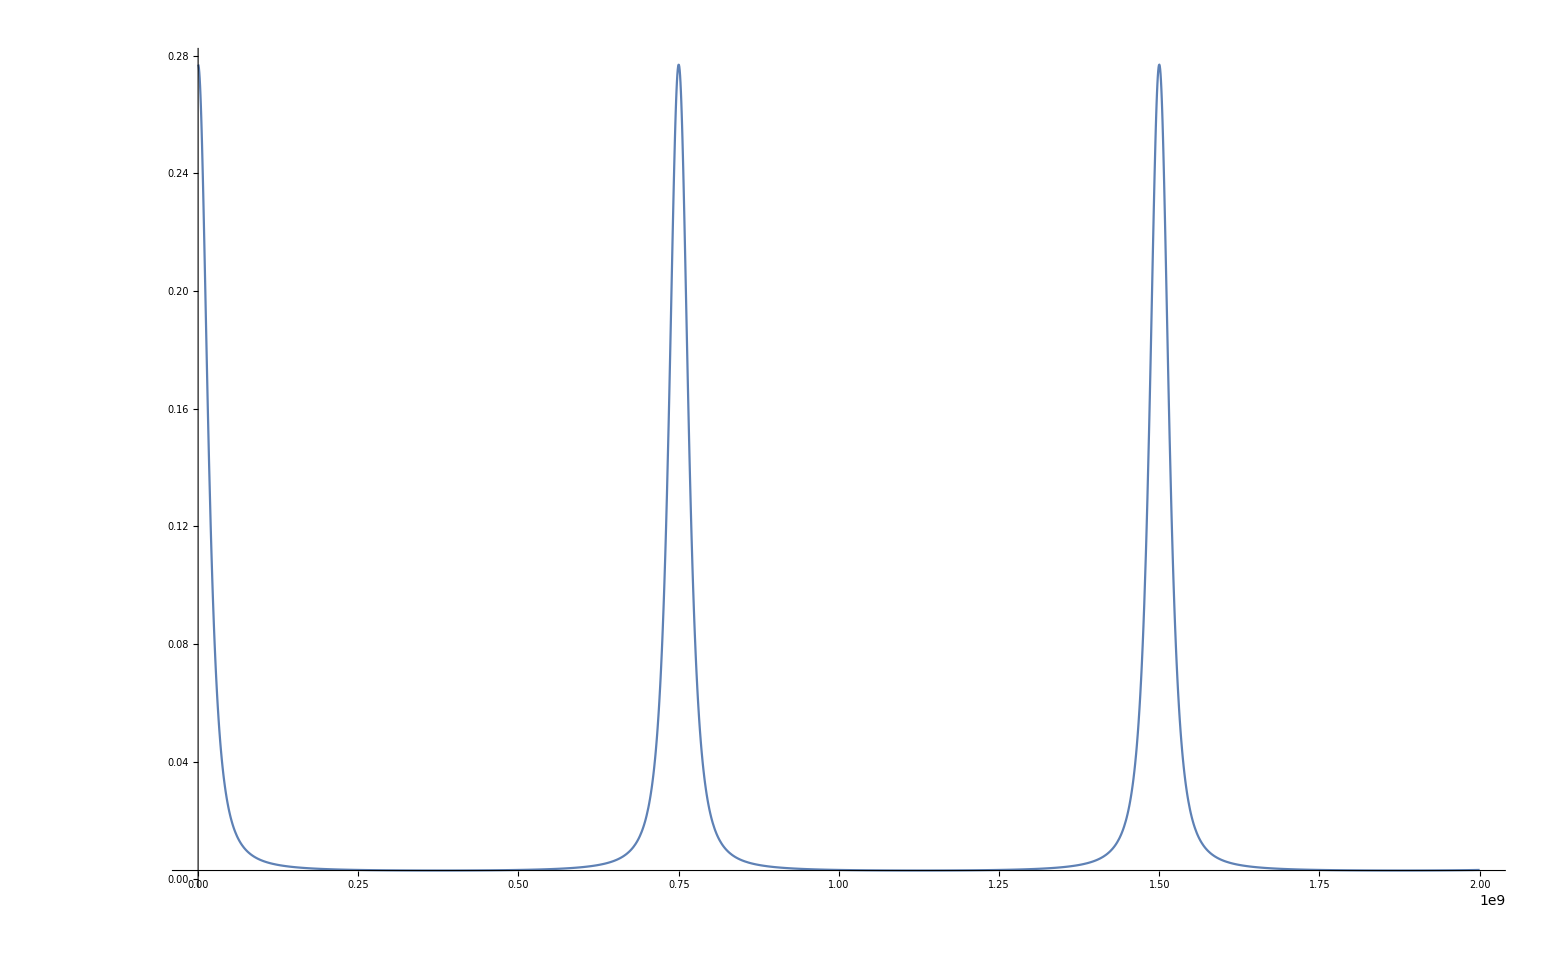

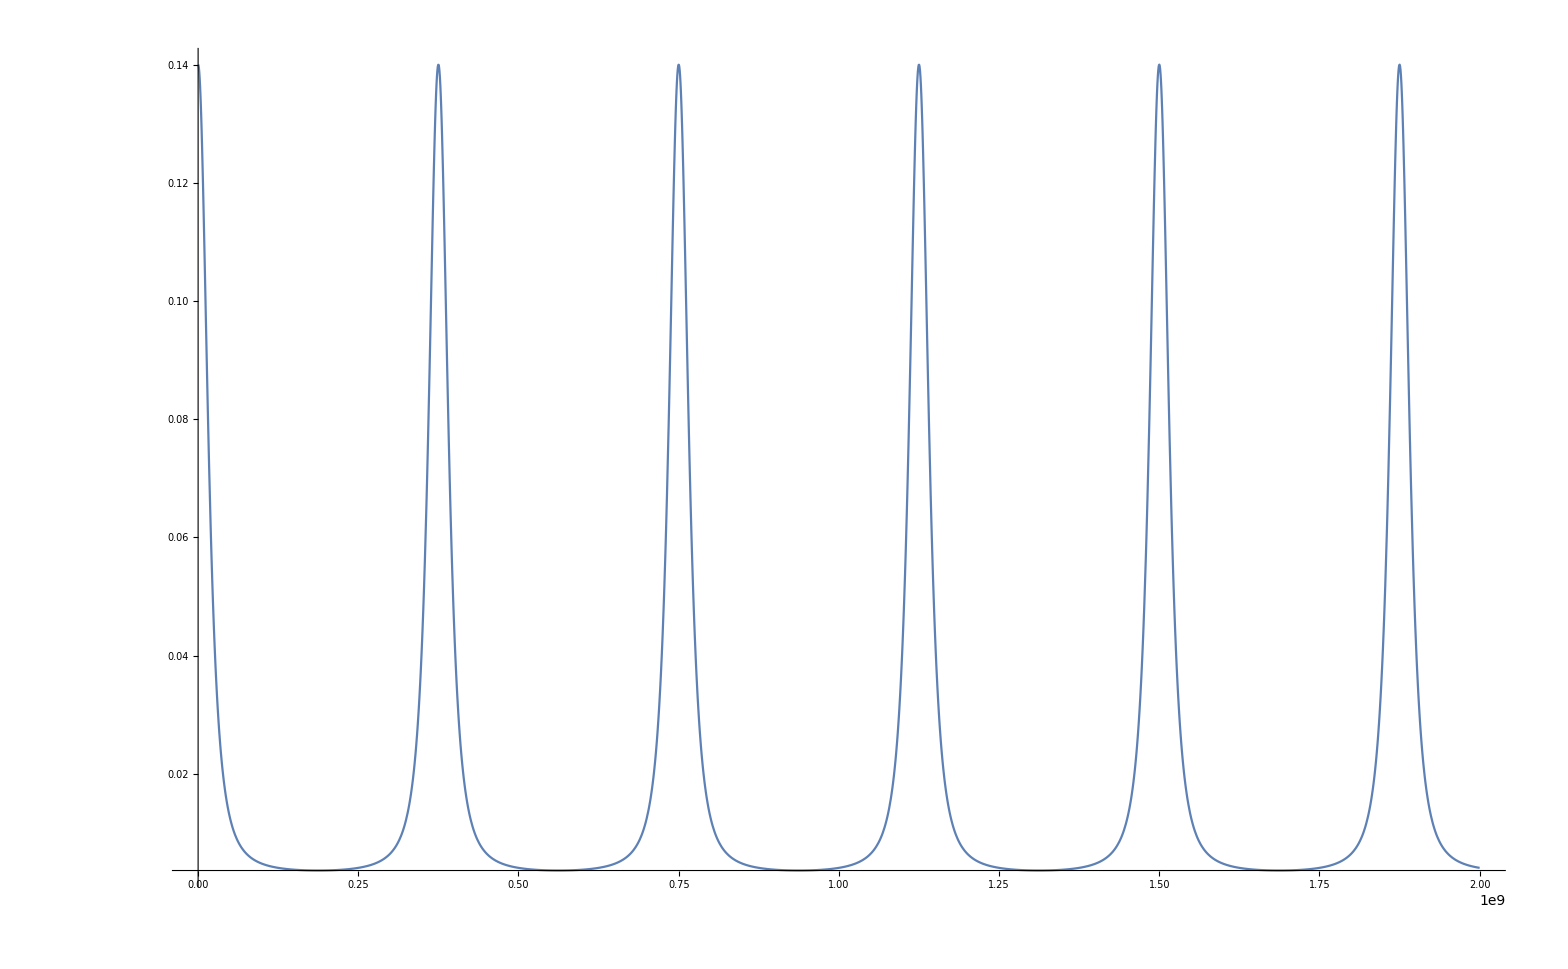

IP[1,1]

```mathematica
R:=0.9
IP[I1_,I2_]:=((1-R)*(I1*Sum[(R^(4 n)) Cos[n 2 π/(3*10^8)*(x-4*n 0.2/(3*10^8)*100*10^9)*4*0.2],{n,0,100}]+I2*Sum[(R^(4n+2)) Cos[(n+0.5) 2 π/(3*10^8)*(x-4*n 0.2/(3*10^8)*100*10^9)*4*0.2 ],{n,0,100}]))^2
Plot[IP[1,1],{x,0,2000000000},PlotRange->Full]
Plot[IP[1,0]+IP[0,1],{x,0,2000000000},PlotRange->Full]
```